```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/WithAngles

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

```mathematica
Ns=1;
sigmas={0.005}(*,0.02,0.05,0.07}*)(*RandomReal[{0,.1},Ns]*)
```

{0.005}

```mathematica
spikyDist=MixtureDistribution[RandomReal[{0.1,1},Ns],Table[MultinormalDistribution[{RandomReal[{-1,1}],RandomReal[{2,10}],RandomReal[{0,10}]},DiagonalMatrix[{sigmas[[i]]/10,sigmas[[i]],sigmas[[i]]}]],{i,1,Ns}]]
```

MultinormalDistribution[{0.542436,4.63402,5.17922},{{0.0005,0.,0.},{0.,0.005,0.},{0.,0.,0.005}}]

```mathematica
Nstars=5000;
```

```mathematica
Dimensions[trueJrL=RandomVariate[spikyDist,Nstars]]
```

{5000,3}

```mathematica
For[i=1,i≤Nstars,i++, While[(Abs[trueJrL[[i,1]]]>1)||(trueJrL[[i,3]]<0),trueJrL[[i]]=RandomVariate[spikyDist]]]
```

```mathematica
Dimensions[trueActions=Transpose[{trueJrL[[All,1]]*trueJrL[[All,2]],trueJrL[[All,2]],trueJrL[[All,3]]}]]
```

{5000,3}

```mathematica
ListPointPlot3D[trueActions,PlotRange->{{-12,12},{-12,12},{0,12}},AspectRatio->1]
```

-Graphics3D-

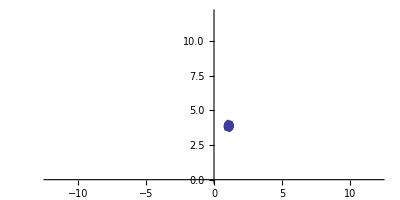

```mathematica
ListPlot[trueActions[[All,{1,3}]],PlotRange->{{-12,12},{0,12}},AspectRatio->1/2]
```

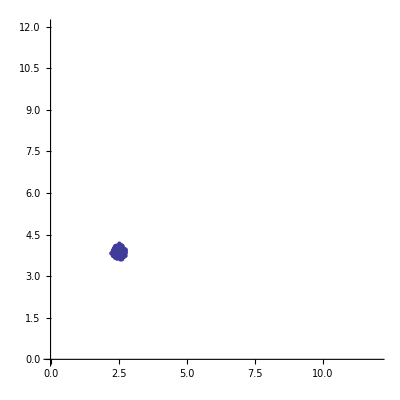

```mathematica
ListPlot[trueActions[[All,{2,3}]],PlotRange->{{0,12},{0,12}},AspectRatio->1]
```

```mathematica
Dimensions[initAngles=Transpose[{RandomVariate[NormalDistribution[1.0,2π/1000],Nstars],RandomVariate[NormalDistribution[2.0,2π/1000],Nstars],RandomVariate[NormalDistribution[6.0,2π/1000],Nstars]}]]
```

{5000,3}

```mathematica
Dimensions[trueAngles=Transpose[{initAngles[[All,1]],initAngles[[All,2]],RandomReal[{0,2π},Nstars]}]]
```

{5000,3}

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"]
```

/data2/users/sanderson/Research/KLStats/Isochrone

```mathematica
link=Install["AAToCart/aa_to_cart_math"]
trueCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
For[i=1, i≤Nstars, i++,trueCart[[i]]=AAToCart[trueActions[[i]],trueAngles[[i]]]]
initCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
For[i=1, i≤Nstars, i++,initCart[[i]]=AAToCart[trueActions[[i]],initAngles[[i]]]]
Uninstall[link]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,28,8]

/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

```mathematica
initPositions=initCart[[All,1;;3]];
initVelocities=initCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
truePositions=trueCart[[All,1;;3]];
trueVelocities=trueCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
ListPointPlot3D[initPositions]
```

-Graphics3D-

```mathematica
ListPointPlot3D[truePositions]
```

-Graphics3D-

```mathematica
ListPointPlot3D[initVelocities]
```

-Graphics3D-

```mathematica
ListPointPlot3D[trueVelocities]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/WithAngles

```mathematica
fnamePosIn="posi.test.dat"
fnameVelIn="veli.test.dat"
```

posi.test.dat

veli.test.dat

```mathematica
pStream=OpenWrite[fnamePosIn,BinaryFormat->False]
vStream=OpenWrite[fnameVelIn,BinaryFormat->False]
Write[pStream,Length[initPositions]];
Export[pStream,initPositions,"Data"];
Export[vStream,initVelocities,"Data"];
Close[pStream]
Close[vStream]
```

OutputStream[posi.test.dat,65]

OutputStream[veli.test.dat,66]

posi.test.dat

veli.test.dat

```mathematica
fnamePosIn="pos.test.dat"
fnameVelIn="vel.test.dat"
```

pos.test.dat

vel.test.dat

```mathematica
pStream=OpenWrite[fnamePosIn,BinaryFormat->False]
vStream=OpenWrite[fnameVelIn,BinaryFormat->False]
Write[pStream,Length[truePositions]];
Export[pStream,truePositions,"Data"];
Export[vStream,trueVelocities,"Data"];
Close[pStream]
Close[vStream]
```

OutputStream[pos.test.dat,87]

OutputStream[vel.test.dat,88]

pos.test.dat

vel.test.dat

```mathematica
link=Install["cartToAA_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/WithAngles/cartToAA_math,29,8]

```mathematica
convJthi=MapThread[CartToAA[12.2,8.0,#1,#2]&,{initPositions,initVelocities}];
```

```mathematica
convJth=MapThread[CartToAA[12.2,8.0,#1,#2]&,{truePositions,trueVelocities}];
```

```mathematica
convJthi[[1]]
```

{2.56889,4.67749,5.18682,2.58147,1.28386,0.29111}

```mathematica
convJth[[1]]
```

{2.56889,4.67749,5.18682,2.58147,3.41935,2.39061}

```mathematica
Uninstall[link]
```

/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/WithAngles/cartToAA_math

```mathematica
convJi=convJthi[[All,1;;3]];
convJ=convJth[[All,1;;3]];
convThi=convJthi[[All,4;;6]];
convTh=convJth[[All,4;;6]];
```

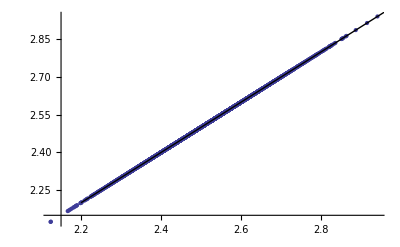

```mathematica
ListPlot[Transpose[{trueActions[[All,1]],convJi[[All,1]]}],Epilog->Line[{{2.2,2.2},{3,3}}]]
```

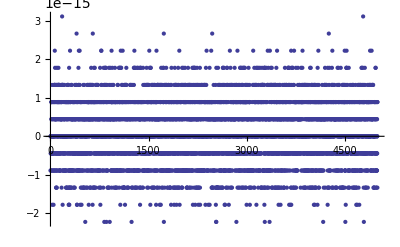

```mathematica
ListPlot[{trueActions[[All,1]]-convJi[[All,1]]},PlotRange->All]
```

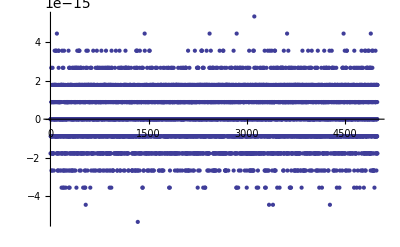

```mathematica
ListPlot[{trueActions[[All,2]]-convJi[[All,2]]},PlotRange->All]
```

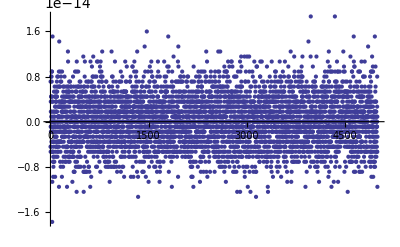

```mathematica
ListPlot[{trueActions[[All,3]]-convJi[[All,3]]},PlotRange->All]
```

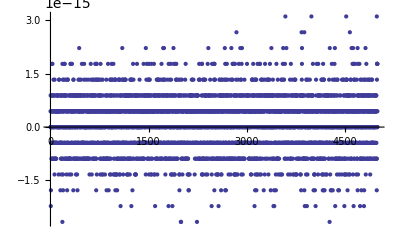

```mathematica
ListPlot[{trueActions[[All,1]]-convJ[[All,1]]},PlotRange->All]
```

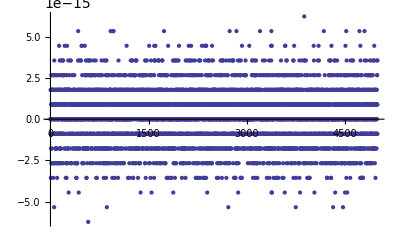

```mathematica
ListPlot[{trueActions[[All,2]]-convJ[[All,2]]},PlotRange->All]
```

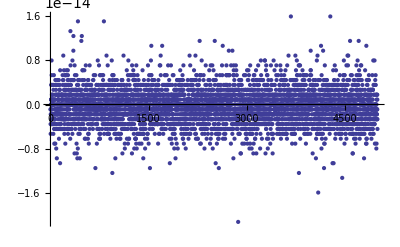

```mathematica
ListPlot[{trueActions[[All,3]]-convJ[[All,3]]},PlotRange->All]
```

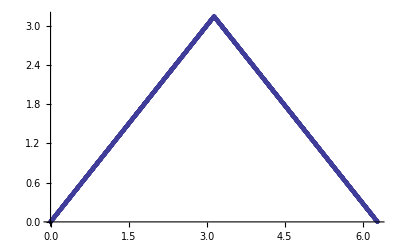

```mathematica
ListPlot[Transpose[{trueAngles[[All,3]],convTh[[All,3]]}]]
```

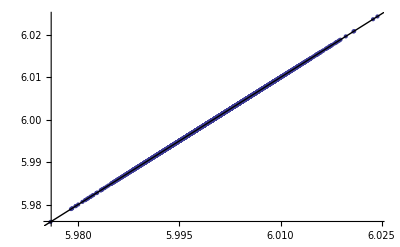

```mathematica
ListPlot[Transpose[{initAngles[[All,3]],2π-convThi[[All,3]]}],Epilog->Line[{{5.9,5.9},{6.1,6.1}}]]
```

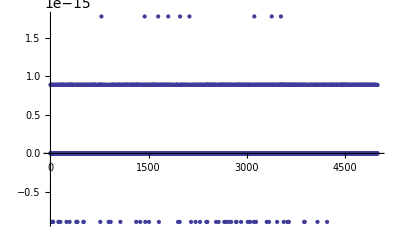

```mathematica
ListPlot[initAngles[[All,3]]-(2π-convThi[[All,3]]),PlotRange->All]
```

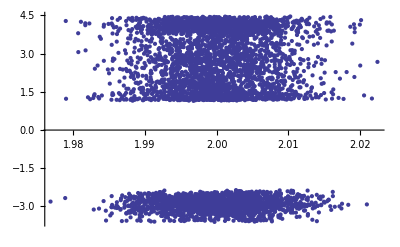

```mathematica
ListPlot[Transpose[{trueAngles[[All,2]],convTh[[All,2]]}]]
```

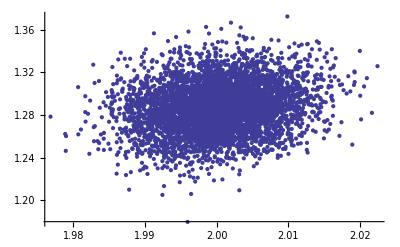

```mathematica
ListPlot[Transpose[{initAngles[[All,2]],convThi[[All,2]]}]]
```

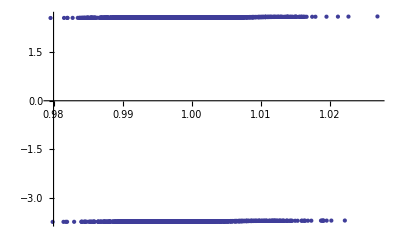

```mathematica
ListPlot[Transpose[{trueAngles[[All,1]],convTh[[All,1]]}]]
```